## Model of yeast making invertase

#### This document includes:

In-patch model, analysis, and figures used for Supplemental discussion 3: “A model of invertase production in yeast exhibits a competition-colonization trade-off”

Code to generate Figure 6E, 6F

```mathematica
ODEs = {
Yeast'==(1-α)γ(Mono + 2 ω Di)*Yeast - d Yeast,
Enz'==α ϵ(Mono + 2 ω Di)*Yeast-d Enz,
Mono'==2 Di Enz-Mono Yeast-d Mono,
Di'==supply-Di Enz-ω Di Yeast - d  Di
};
params={
d->0.5,
supply->1,
ω->0.1,
γ->1,
ϵ->2
};
```

### Extinction equilibrium

```mathematica
Solve[Map[0==#[[2]]&,ODEs]/.{Yeast->0}, {Enz, Mono, Di}]
```

{{Enz→0,Mono→0,Di→supply/d}}

#### Jacobian

```mathematica
rhs =Map[Last,ODEs]
jac=Map[D[rhs, #]&, {Yeast, Enz, Mono, Di}];
Simplify[jac]//MatrixForm
```

{-d Yeast+Yeast (1-α) γ (Mono+2 Di ω),-d Enz+Yeast α ϵ (Mono+2 Di ω),2 Di Enz-d Mono-Mono Yeast,-d Di-Di Enz+supply-Di Yeast ω}

(-d-(-1+α) γ (Mono+2 Di ω) | α ϵ (Mono+2 Di ω) | -Mono | -Di ω
0 | -d | 2 Di | -Di
-Yeast (-1+α) γ | Yeast α ϵ | -d-Yeast | 0
-2 Yeast (-1+α) γ ω | 2 Yeast α ϵ ω | 2 Enz | -d-Enz-Yeast ω)

```mathematica
Eigenvalues[jac/.{Yeast->0,Enz->0,Mono->0,Di->supply/d}]
```

{-d,-d,-d,(-d^2+2 supply γ ω-2 supply α γ ω)/d}

stability depends on the parameters

### NonNegativeReal solutions

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

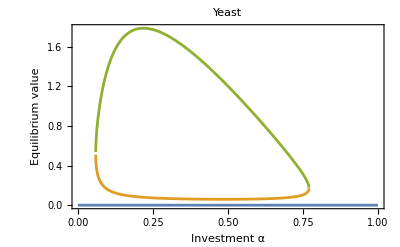
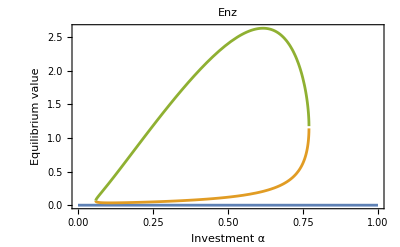
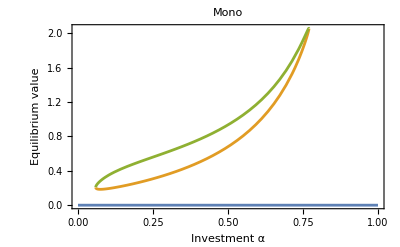
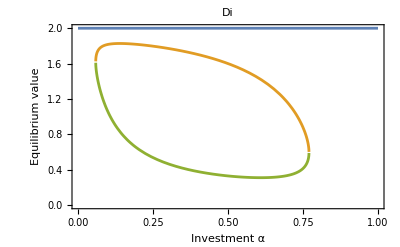

```mathematica
numSol=Solve[Map[0==#[[2]]&,ODEs]/.params, {Yeast, Enz, Mono, Di},NonNegativeReals];
Table[Plot[Evaluate[var/.numSol/.{α->a}/.params],{a,0, 1},PlotLabel->ToString[var],
Frame->True,FrameLabel->{"Investment α","Equilibrium value"}],{var,{Yeast, Enz, Mono, Di}}]
```

```mathematica
numSol/.{α->0.1}
```

{{Yeast→0,Enz→0,Mono→0,Di→2.},{Yeast→0.156037,Enz→0.034675,Mono→0.192103,Di→1.81726},{Yeast→1.39224,Enz→0.309386,Mono→0.344721,Di→1.05417}}

Stable is solution 3. Maximum:

```mathematica
Maximize[{numSol[[3]][[1]][[2]][[1]], 0.1<α<0.7},α,PositiveReals]
```

{1.78798,{α→0.218274}}

Bifurcation

```mathematica
numSol[[3]][[1]][[2]][[2]]
```

0.0590707<α<0.769965

```mathematica
numSol[[3]][[1]]/.α->0.0590707+0.000001
```

Yeast→0.526848

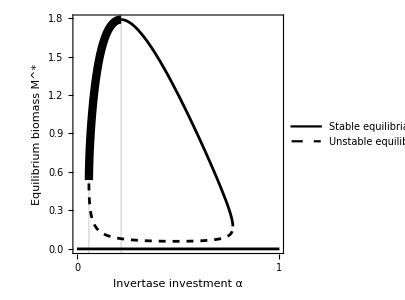

```mathematica
lines=Evaluate[Yeast/.numSol];
stable=lines[[3]];
lines[[3]]=ConditionalExpression[stable,α>0.218274];
AppendTo[lines, ConditionalExpression[stable,α<0.218274]];
pltvsalpha=Plot[lines,{α,0,1},
PlotStyle->{Black,{Black,Dashed},Black, {Black,Thickness[0.02]}},
Frame->True,FrameLabel->{"Invertase investment α","Equilibrium biomass M^*"},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],LabelStyle->Directive[FontSize->11,FontColor->Black],
PlotLegends->Placed[LineLegend[{Black,{Black,Dashed}},{"Stable equilibria", "Unstable equilibrium"},LegendMarkerSize->{22,10}],{Right,Top}],
PlotRangeClipping->False,
Prolog->{
Directive[LightGray],
Line[{{0.0590707,-0.06},{0.0590707,0.526848}}],
Line[{{0.218274,-0.06},{0.218274,1.78798}}],
Black,FontSize->11,
Text["α_min",{0.0590707+0.02,-0.17}],
Text["α̂",{0.218274,-0.16}]
},
FrameTicks->{{Automatic,None},{{0,1},None}},
ImageSize->300,AspectRatio->1
]
```

#### CC trade-off

```mathematica
Mstar[a_]:=Yeast/.numSol[[3]]/.α->a
Rstar[a_]:=1/(1-α) /.α->a
```

```mathematica
Mstar[0.09]
```

1.28307

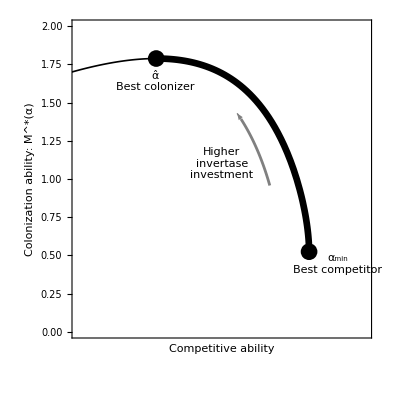

```mathematica
Show[ParametricPlot[Evaluate@{1/Rstar[a],Mstar[a]},{a,0.0590707,0.218274}, (* frontier *)
PlotStyle->{Black, Thickness[0.012]},
PlotRange->{{0.7,1},{0,2}},
Frame->True,FrameLabel->{"Competitive ability","Colonization ability: M^*(α)"},
FrameTicks->{{Automatic,None},{None,None}},
PlotTheme->"Default",BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontSize->13,FontColor->Black],AspectRatio->1,
Epilog->{
Directive[PointSize[0.03]],
Point[{1/Rstar[a],Mstar[a]}/.a->0.0590707+0.0000001],
Text["α_min\nBest competitor",{1/Rstar[a]+0.03,Mstar[a]-0.08}/.a->0.0590707+0.0000001,{1,0}],
Point[{1/Rstar[a],Mstar[a]}/.a->0.218274],
Text["α̂\nBest colonizer",{1/Rstar[a]-0.001,Mstar[a]-0.15}/.a->0.218274],
Directive[Gray],
Arrow[{{1/Rstar[a]-0.03,Mstar[a]}/.(a->0.1), {1/Rstar[a]-0.03,Mstar[a]}/.(a->0.104)}],
Directive[Black,FontSize->11],
Text["Higher\ninvertase\ninvestment",{0.85,1.1}]
},
ImageSize->{300}
],
ParametricPlot[Evaluate@{1/Rstar[a],Mstar[a]},{a,0.218274,0.4},PlotStyle->{Black,Thickness[0.003]}],
ParametricPlot[Evaluate@{1/Rstar[a]-0.03,Mstar[a]},{a,0.07,0.10},PlotStyle->Gray] (* arrow*)
]
```

### ZNGIs

```mathematica
tolIridescent = Map[RGBColor,{"#FEFBE9","#FCF7D5","#F5F3C1","#EAF0B5","#DDECBF","#D0E7CA","#C2E3D2","#B5DDD8","#A8D8DC","#9BD2E1","#8DCBE4","#81C4E7","#7BBCE7","#7EB2E4","#88A5DD","#9398D2","#9B8AC4","#9D7DB2","#9A709E","#906388","#805770","#684957","#46353A"}];
colors=tolIridescent[[{7,10,13,16,19,22}]]
```

{RGBColor[0.7607843137254902, 0.8901960784313725, 0.8235294117647058],RGBColor[0.6078431372549019, 0.8235294117647058, 0.8823529411764706],RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353]}

```mathematica
zngi = 0 ==(1-α)γ(Mono + 2 ω Di) - d;
```

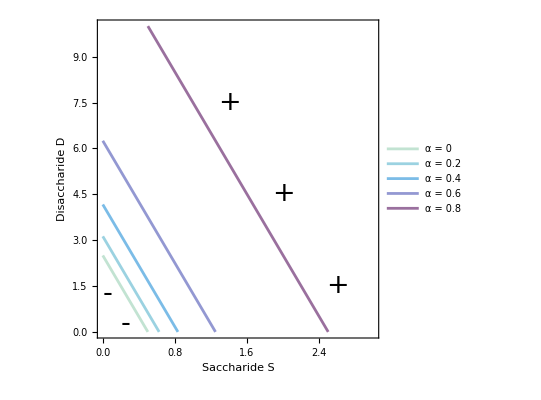

```mathematica
ContourPlot[
Evaluate[Table[
zngi/.params,
{α,{0,0.2,0.4,0.6,0.8}}
]]
,{Mono,0,3},{Di,0,10},
ContourStyle->colors,
PlotLegends->Placed[
Map["α = "<>ToString[#]&,{0,0.2,0.4,0.6,0.8}],
{Right,Top}],
BaseStyle->Directive[FontSize->13,FontColor->Black],
LabelStyle->Directive[FontColor->Black],
Epilog->{
Black,Text[Style["-",27],{0.25,0.25}],
Black,Text[Style["-",27],{0.05,1.25}],
Black,Text[Style["+",27],{2.6,1.5}],
Black,Text[Style["+",27],{2,4.5}],
Black,Text[Style["+",27],{1.4,7.5}]
},
Frame->True,FrameLabel->{"Saccharide S","Disaccharide D"}]
```